## functions

```mathematica
Import["~/Code/cytomod/analysis/cytomod_functions.m"];
```

```mathematica
meanorzero[x_]:=If[Length[x]>0,Mean[x],0];
errorzero[x_]:=If[Length[x]>1,StandardDeviation[x]/Sqrt[Length[x]],0];

doublyBound[m_]:=Cases[m,_?((#[[5]]!=-1&&#[[6]]!=-1)&),1,Heads->False];
divorzero[x_,y_]:=If[y≠0,x/y,0];
myrijP[x_,zpos_,fov_]:=Join[rijP[x[[1;;2]]-zpos[[1;;2]],fov],x[[3;;]]];
constFun[l_,x_]:={l,ConstantArray[x,Length[l]]}ᵀ;
riffleNones[l_]:=Riffle[Riffle[l,None],None,3];



fs=Directive[Opacity[1],Thickness[0.01]];
forestgreen=RGBColor[34/255,139/255,34/255];
skyblue=RGBColor[135/255,206/255,250/255];
cols={Red,Darker[Cyan]};
c1[x_]:=Style[ToString[x],cols[[1]]];
c2[x_]:=Style[ToString[x],cols[[2]]];
vline[th_]:=Graphics[{Thickness[th],Line[{{0,-1},{0,1}}]}];
```

```mathematica
pss=Flatten[ConstantArray[#,3]&/@cols];
```

### functions for drawing lattices

```mathematica
latticeFromDomain[x_,ll_:0.037,lf_:25]:=If[Length[x]>0,Round[Range[x[[1]],x[[-1]],ll]/ll],Nothing];

fullLatFromAllDomains[doms1_,doms2_,lf_:25,lb_:0.037]:=Module[{},
x=ConstantArray[0,Ceiling[lf/lb]];
x[[Flatten[doms1]+1]]=1;
x[[Flatten[doms2]+1]]=2;
x
];

fullLatFromManyDomains[domsarr_,lf_:25,lb_:0.037]:=Module[{},
x=ConstantArray[0,Ceiling[lf/lb]];
Do[x[[Flatten[domsarr[[i]]]+1]]=i,{i,Length[domsarr]}];
x
];
```

### filenames and directories

```mathematica
headdir=outdir<>"/xlink_segregation/spacers";
headdirL=outdir<>"/xlink_segregation/lattice";
figdir=outdir<>"/xlink_segregation/figs/paper";

doms={"1","2"};
domfs="/analysis/spacer"<>ToString[#]<>"_domains_t1-2000_nc4_rc1.dat"&/@doms;
(*domfsf0="/analysis/spacer"<>ToString[#]<>"_domains_f0_t1-2000_nc4_rc1.dat"&/@doms;*)
domfsL="/analysis/spacer"<>ToString[#]<>"_domains_t9000-10000_nc4_rc1.dat"&/@doms;
angf="/analysis/ang_bw_fils.dat";

todeletedirs=Import["~/Code/cytomod/spacer_metadata/sim_results/crashed_list.txt","Table"][[All,1]];
```

### calclulating gap lengths

```mathematica
gaplengths[s1doms_,s2doms_]:=Module[{},
If[
Length[s1doms]==0||Length[s2doms]==0,
gls={},
domeps=Join[s1doms[[All,1]],s1doms[[All,2]],s2doms[[All,1]],s2doms[[All,2]]];
domeplabs= Join[ConstantArray[1,2*Length[s1doms]],ConstantArray[2,2*Length[s2doms]]];
sort=Ordering[domeps];
gapPoss=Flatten[Position[Differences[domeplabs[[sort]]],_?((#≠0)&)]];
gls=Differences[domeps[[sort]]][[gapPoss]]
];
gls
];
```

```mathematica
ptsdb[dir_,n_]:=
If[
FileExistsQ[dir<>"/txt_stack/spacers"<>ToString[n]<>"_bound.txt"],
pts4[dir,"spacers"<>ToString[n]<>"_bound"],
With[{s1s=pts2[dir,"spacers"<>ToString[n]]},Table[Cases[s1s[[t,All]],_?((#[[5]]!=-1&&#[[6]]!=-1)&),1,Heads->False],{t,Length[s1s]}]]
];
ClearAll[makeCenteredMovieRow];
makeCenteredMovieRow[dirs_,outf_]:=Module[{},
links=pts4[#,"links"]&/@dirs;
conn1s=ptsdb[#,1]&/@dirs;
conn2s=ptsdb[#,2]&/@dirs;

linkz=Table[Map[myrijP[#,links[[i,1,7,1;;2]],{35,20}]&,links[[i]],{2}],{i,Length[idxs]}];
conn1z=Table[Map[myrijP[#,links[[i,1,7,1;;2]],{35,20}]&,conn1s[[i]],{2}],{i,Length[idxs]}];
conn2z=Table[Map[myrijP[#,links[[i,1,7,1;;2]],{35,20}]&,conn2s[[i]],{2}],{i,Length[idxs]}];

mov=Table[drawmixed[{},linkz[[i]],conn1z[[i]],conn2z[[i]],"",False,{35,20},False,26,Green,Red,Darker[Cyan],White,"",-1,3,False],{i,Length[idxs]}];

trimovie=Table[GraphicsRow[Table[mov[[i,t]],{i,Length[idxs]}],Frame->All,Spacings->0],{t,Dimensions[mov][[2]]}];

Export[figdir<>"/"<>outf<>".avi",trimovie[[1;;-1;;5]],ImageResolution->250];
];
```

```mathematica
se6func="/seed"<>ToString[#]<>"e6"&;
se7func="/seed"<>ToString[#]<>"e7"&;
```

```mathematica
ClearAll[DomainLengthAverager];
DomainLengthAverager[
vars1_,tiFunc_,winlen_,
topdir_,paramStrFcn_,
outstrFcn_,tWindir_,avgdldir_,
domfs_,seedStrFcn_,isAfines_:True,
doms_:{1,2},angThresh_:0.8,
dirsuf_:"/",parallelize_:True]:=
Module[{},

twdir = topdir<>tWindir<>dirsuf;
avgdir=topdir<>avgdldir<>dirsuf;

Print["Creating directory "<>twdir];
Print["Creating directory "<>avgdir];

CreateDirectory[twdir];
CreateDirectory[avgdir];
doer=If[parallelize,ParallelDo,Do];
seeds=Range[20];

doer[
dirs=Table[StringJoin[ToString/@{topdir,seedStrFcn[sd],paramStrFcn[var]}],{sd,seeds}];
ti=tiFunc[var];
If[isAfines,
dirs=DeleteCases[dirs,Apply[Alternatives,todeletedirs],{1}];
angs=Map[importCheck[#<>angf]&,dirs,{1}];
s1minang=Table[Min[angs[[i,ti;;(ti+winlen),1]]],{i,Length[angs]}];
deleteIndices=Position[s1minang,_?((#<angThresh)&),{1},Heads->False];dirs=Delete[dirs,deleteIndices];
];

s1doms=Map[importCheck[#<>domfs[[dom]]]&,dirs,{1}];
s1domlens=Table[
If[Length[s1doms[[i,t,1]]]>0,s1doms[[i,t,1,All,-1]]-s1doms[[i,t,1,All,1]],{}]
,{i,Length[s1doms]},{t,ti,ti+winlen}];

s1domlenmus=Map[meanorzero[Flatten[#]]&,s1domlens];
s1domlenbar=meanorzero[s1domlenmus];
s1domlenerr=errorzero[s1domlenmus];

fname=StringJoin[ToString/@{outstrFcn[var],"_doms",dom,".dat"}];
outf1=twdir<>fname;
Export[outf1,Map[NumberForm[#,6]&,s1domlens,{2}],"Table"];

outf2=avgdir<>fname;
Export[outf2,{s1domlenbar,s1domlenerr,Length[s1doms]}];,

{dom,doms},
{var,vars1}
]
];
```

## fig 1 : afines can make domains

```mathematica
s1denss={0.083,0.125,0.168,0.250,0.300,0.375,0.500,0.750};
s2dens=0.25;
densrats=s1denss/s2dens;
s1densstrs=Map[NumberForm[#,{3,3}]&,s1denss];
dirs=Table[StringJoin[ToString/@{
outdir,"/xlink_segregation/spacers/s1dens_lgrow0_s2len0.3_s2init_dt0.00002/seedC/s1dens",dens
}],{dens,s1densstrs}];
densratstrs=ToString[NumberForm[#,{2,2}]]&/@densrats;
t=2000;
```

### movies

```mathematica
idxs={2,4,7};
```

```mathematica
links=pts4[#,"links"]&/@(dirs[[idxs]]);
conn1s=pts4[#,"spacers1_bound"]&/@(dirs[[idxs]]);
conn2s=pts4[#,"spacers2_bound"]&/@(dirs[[idxs]]);
```

```mathematica
linkz=Table[Map[myrijP[#,links[[i,1,7,1;;2]],{35,20}]&,links[[i]],{2}],{i,Length[idxs]}];
conn1z=Table[Map[myrijP[#,links[[i,1,7,1;;2]],{35,20}]&,conn1s[[i]],{2}],{i,Length[idxs]}];
conn2z=Table[Map[myrijP[#,links[[i,1,7,1;;2]],{35,20}]&,conn2s[[i]],{2}],{i,Length[idxs]}];
```

```mathematica
mov=Table[drawmixed[{},linkz[[i]],conn1z[[i]],conn2z[[i]],"",False,{35,20},False,26,Green,Red,Darker[Cyan],White,"",-1,3,False],{i,Length[idxs]}];
```

```mathematica
trimovie=Table[GraphicsRow[{mov[[1,t]],mov[[2,t]],mov[[3,t]]},Frame->All,Spacings->0],{t,Dimensions[mov][[2]]}];
```

```mathematica
(*Manipulate[Show[trimovie[[t]]],{t,1,Length[trimovie],1}]*)
```

```mathematica
Export[figdir<>"/diff100_densrats0-5_1_2.avi",trimovie[[1;;-1;;5]],ImageResolution->250];
```

### frames

```mathematica
t=2000;
links=pts4[#,"links"][[t]]&/@dirs;
```

```mathematica
conn1s=doublyBound[pts4[#,"spacers1_bound"][[t]]]&/@dirs;
conn2s=doublyBound[pts4[#,"spacers2_bound"][[t]]]&/@dirs;
```

```mathematica
frs1=drawmixed[{},links,conn1s,conn2s,"",False,{35,20},False,26,Green,Red,Darker[Cyan]];
```

```mathematica
(*centering filaments and xlinks to middle of frame*)
zeros=Table[Join[links[[i,1,1;;2]],{0,0}],{i,Length[links]}];
fov={35,20};

lc=Table[Join[rijP[(links[[i,l,1;;2]]-links[[i,1,1;;2]]),fov],links[[i,l,3;;]]],{i,Length[links]},{l,Length[links[[i]]]}];
s1c=Table[Join[rijP[(conn1s[[i,l,1;;2]]-links[[i,1,1;;2]]),fov],conn1s[[i,l,3;;]]],{i,Length[conn1s]},{l,Length[conn1s[[i]]]}];
s2c=Table[Join[rijP[(conn2s[[i,l,1;;2]]-links[[i,1,1;;2]]),fov],conn2s[[i,l,3;;]]],{i,Length[conn2s]},{l,Length[conn2s[[i]]]}];
```

```mathematica
(*frs=Table[drawmixed[{},links[[i]],conn1s[[i]],conn2s[[i]],"",False,{35,20},False,26,Green,Red,Darker[Cyan]],{i,Length[links]}];*)
```

```mathematica
frsc=drawmixed[{},lc,s1c,s2c,"",False,{35,20},False,26,Green,Red,Darker[Cyan],"",White,-1,3,False];
```

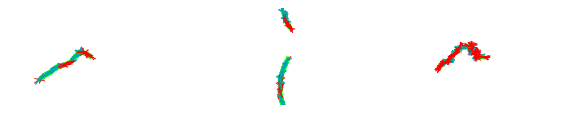

```mathematica
GraphicsRow[frsc[[{3,4,7}]],ImageSize->Large]
```

```mathematica
fdir=figdir<>"/mar19/diff100_t2000_frames_centered";
CreateDirectory[fdir];
Do[Export[fdir<>"/densrat"<>densratstrs[[i]]<>".eps",frsc[[i]]],{i,Length@densrats}];
```

### domain calculation

```mathematica
dom1s=Map[ToExpression,importCheck[#<>domfs[[1]]]&/@dirs,{3}][[All,t]];
dom2s=Map[ToExpression,importCheck[#<>domfs[[2]]]&/@dirs,{3}][[All,t]];
```

```mathematica
latdoms1=Map[latticeFromDomain,dom1s[[All,1]],{2}];
latdoms2=Map[latticeFromDomain,dom2s[[All,1]],{2}];
```

```mathematica
latsT=Table[fullLatFromAllDomains[latdoms1[[i]],latdoms2[[i]]],{i,Length[densrats]}];
```

```mathematica
lattices=Import[#<>"/lattice.dat","CSV"][[-1]]&/@dirs;
```

```mathematica
lattices2=Table[lattice/.{1->4,2->5},{lattice,lattices}];
lattices3=lattices2+latsT[[All,1;;Dimensions[lattices][[2]]]];
```

```mathematica
maxl=15;
```

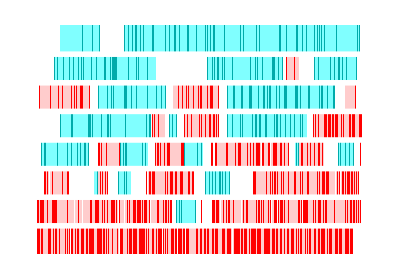

```mathematica
p1=ArrayPlot[lattices3(*[[2;;-2]]*),AspectRatio->0.7,FrameLabel->{"ρ_short/ρ_long","position (μm)"},DataRange->{{0,maxl},{1,Length[densrats](*-2*)}},BaseStyle->Directive[FontSize->22,FontColor->Blue],
(*ColorRules->{5->Black,7->Green,1->Gray,2->(*Darker[Green]*)forestgreen,0->White},*)
ColorRules->{5->Red,7->Darker[Cyan],1->Blend[{Red,White},0.8],2->Blend[{Cyan,White},0.5],0->White,4->White,6->White},
BaseStyle->{FontFamily->"Arial",FontSize->22,SingleLetterItalics->False},FrameStyle->Black,FrameTicks->{{Range[Length[densrats](*-2*),1,-1],densratstrs(*[[2;;-2]]*)}ᵀ,Range[0,25,5]},GridLines->{None,Range[1,Length[densrats]-1]+0.5},GridLinesStyle->Directive[White,Thickness[0.01]],Method->{"GridLinesInFront"->True}]
```

```mathematica
Export[figdir<>"/mar19/domains_and_spacers_vs_densrat_ldiff100_t2000.eps",p1];
```

```mathematica
{{Export[figdir<>"/domains_and_spacers_vs_densrat_ldiff100_lgrow0_denstot0.5.eps",p1];}, {Export[figdir<>"/domains_and_spacers_vs_densrat_ldiff100_lgrow0_denstot0.5.png",p1];}}
```

## fig 2 : simulation and lattice for mechanical constraints (dx and lp)

```mathematica
seeds=Range[20];
s1dens="0.25";
s2dens="0.25";
```

### lgrow = 0, dx varying

```mathematica
dxs={"0.000","0.027","0.05","0.1","0.3","0.5","1"};
dxns=1000*(ToExpression/@dxs);
dxns[[1]]=10;
```

#### averaging over seeds -- afines

```mathematica
job1="/ldiff_calib_s1init";
job2="/ldiff_calib_s2init";

ti=1900;
winlen=100;

avgdldir="/dom_lens/avg_err_ns_ti"<>ToString[ti]<>"_wl"<>ToString[winlen]<>"c";
t100dir="/dom_lens/ti"<>ToString[ti]<>"_wl"<>ToString[winlen]<>"c";
```

```mathematica
DomainLengthAverager[dxs,ti&,winlen,headdir<>job1,("/ldiff"<>#)&,("ldiff"<>#)&,t100dir,avgdldir,domfs,se7func];
```

Creating directory /project/weare-dinner/simonfreedman/cytomod/out/xlink_segregation/spacers/ldiff_calib_s1init/dom_lens/ti1900_wl100c/

Creating directory /project/weare-dinner/simonfreedman/cytomod/out/xlink_segregation/spacers/ldiff_calib_s1init/dom_lens/avg_err_ns_ti1900_wl100c/

CreateDirectory::filex: /project/weare-dinner/simonfreedman/cytomod/out/xlink_segregation/spacers/ldiff_calib_s1init/dom_lens/ti1900_wl100c/ already exists.

CreateDirectory::filex: /project/weare-dinner/simonfreedman/cytomod/out/xlink_segregation/spacers/ldiff_calib_s1init/dom_lens/avg_err_ns_ti1900_wl100c/ already exists.

```mathematica
DomainLengthAverager[dxs,ti&,winlen,headdir<>job2,"/ldiff"<>#&,("ldiff"<>#)&,t100dir,avgdldir,domfs,se7func];
```

Creating directory /project/weare-dinner/simonfreedman/cytomod/out/xlink_segregation/spacers/ldiff_calib_s2init/dom_lens/ti1900_wl100c/

Creating directory /project/weare-dinner/simonfreedman/cytomod/out/xlink_segregation/spacers/ldiff_calib_s2init/dom_lens/avg_err_ns_ti1900_wl100c/

```mathematica
(*importing simulation data*)
datfs=Table[StringJoin[ToString/@{headdir,job,avgdldir,"/ldiff",dx,"_doms",dom,".dat"}],{job,{job1,job2}},{dom,doms},{dx,dxs}];
dps=Map[importCheck[#][[All,1]]&,datfs,{3}];

avgdps=0.5(dps[[1]]+dps[[2]]);
errscaled=dps[[All,All,All,2]]/dps[[All,All,All,1]];
s1doms=errcurves[dxns,avgdps[[1,All,1]],avgdps[[1,All,1]]*Sqrt[errscaled[[1,1]]^2+errscaled[[2,1]]^2]];
s2doms=errcurves[dxns,avgdps[[2,All,1]],avgdps[[2,All,1]]*Sqrt[errscaled[[1,2]]^2+errscaled[[2,2]]^2]];

avgdps=0.25(dps[[1,1]]+dps[[1,2]]+dps[[2,1]]+dps[[2,2]]);
sdoms=errcurves[Log10@dxns,avgdps[[All,1]],avgdps[[All,1]]*Sqrt[errscaled[[1,1]]^2+errscaled[[2,1]]^2+errscaled[[1,2]]^2+errscaled[[2,2]]^2]];
```

#### averaging over seeds -- lattice

```mathematica
job="/len15_lp17.000_mu2-0.008_munn0.000";
dxs={"0.000","0.027","0.05","0.1","0.5","1"}; (*forgot to do 0.3 for lattice -- FIX*)
dxns=1000*(ToExpression/@dxs);
dxns[[1]]=10;
```

```mathematica
ti=1; (*domains are only computed from t=9000 onward (to t=10000)*)
winlen=1000;

avgdldir="/dom_lens/avg_err_ns_ti"<>ToString[ti]<>"_wl"<>ToString[winlen]<>"b";
t100dir="/dom_lens/ti"<>ToString[ti]<>"_wl"<>ToString[winlen]<>"b";

DomainLengthAverager[dxs,ti&,winlen,headdirL<>job,("/lendiff"<>#<>"_mu1-0.00800")&,("dx"<>#)&,t100dir,avgdldir,domfsL,se6func,False];
```

Creating directory /project/weare-dinner/simonfreedman/cytomod/out/xlink_segregation/lattice/len15_lp17.000_mu2-0.008_munn0.000/dom_lens/ti1_wl1000b/

Creating directory /project/weare-dinner/simonfreedman/cytomod/out/xlink_segregation/lattice/len15_lp17.000_mu2-0.008_munn0.000/dom_lens/avg_err_ns_ti1_wl1000b/

CreateDirectory::filex: /project/weare-dinner/simonfreedman/cytomod/out/xlink_segregation/lattice/len15_lp17.000_mu2-0.008_munn0.000/dom_lens/ti1_wl1000b/ already exists.

CreateDirectory::filex: /project/weare-dinner/simonfreedman/cytomod/out/xlink_segregation/lattice/len15_lp17.000_mu2-0.008_munn0.000/dom_lens/avg_err_ns_ti1_wl1000b/ already exists.

```mathematica
(*importing lattice data*)
topdirL=headdirL<>"/"<>job;
datfs=Table[StringJoin[ToString/@{topdirL,avgdldir,"/dx",dx,"_doms",dom,".dat"}],{dx,dxs},{dom,1,2}];
dps=Map[importCheck[#][[All,1]]&,datfs,{2}];
avglens=0.5(dps[[All,1,1]]+dps[[All,2,1]]);
errscaled=dps[[All,All,2]]/dps[[All,All,1]];
domlensL=errcurves[Log10@dxns,avglens,avglens*Sqrt[errscaled[[All,1]]^2+errscaled[[All,2]]^2]];
s1domsL=errcurves[dxns,dps[[All,1,1]],dps[[All,1,2]]];
s2domsL=errcurves[dxns,dps[[All,2,1]],dps[[All,2,2]]];
```

#### plotting

fig 2 b

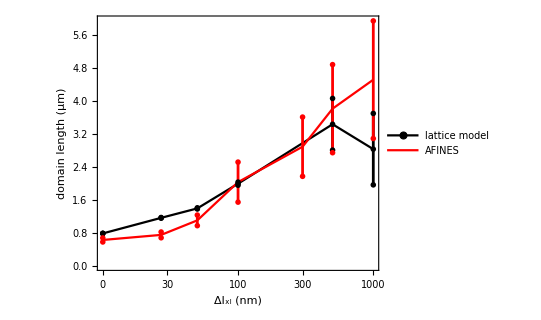

```mathematica
ltbase=LogTicks[-1,5,ShowTickLabels->False,MinorTickLength->0.008];
myticks=Join[Range[10],Range[20,100,10],Range[200,1000,10]];
cols={Black,Red,Darker[Cyan]};
labels={(*,"AFINES (long)",*) "lattice model","AFINES"};
pms=Join[
errbarpms[cols[[1]],Disk[],0.04],
errbarpms[cols[[2]],{Transparent,EdgeForm[Directive[Thick,cols[[2]]]],Rectangle[]}],
errbarpms[cols[[2]],{Transparent,EdgeForm[Directive[Thick,cols[[2]]]],Disk[]}]
];

p1=ListPlot[Join[domlensL,sdoms],
PlotRange->Full,
PlotStyle->Flatten[ConstantArray[#,3]&/@cols],
FrameLabel->{"Δl_xl (nm)","domain length (μm)"},
Joined->{True,False,False},
PlotMarkers->pms,
Filling->Flatten[Table[{i->{i+1}},{i,2,15,3}]],
FillingStyle->fs,
PlotLegends->Placed[LineLegend[riffleNones[labels],LegendLayout->"Column",LegendMarkers->riffleNones[pms[[1;;-1;;3]]],Spacings->0,LegendMarkerSize->{30,15},LabelStyle->FontSize->18],{0.45,0.8}(*Right*)],
FrameTicks->{{Automatic,Automatic},{Join[ltbase,{{Log10@10,"0"},{Log10@30,30},{Log10@100,100},{Log10@300,300},{Log10@1000,1000}}],Automatic}}]
```

```mathematica
Export[figdir<>"/mar19/dx_vs_dl_afines_lattice.eps",p1];
Export[figdir<>"/mar19/fig2b.eps",p1];
```

fig s2

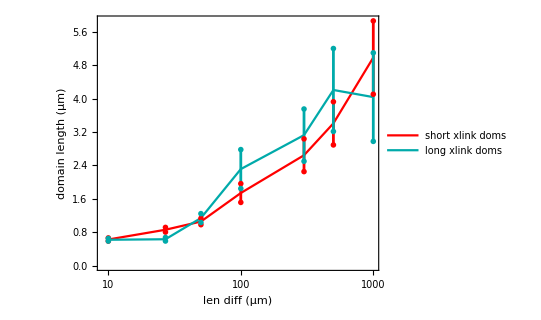

```mathematica
cols={Red,Darker[Cyan]};
labels={ "short xlink doms", "long xlink doms"};
pms=Join[
errbarpms[cols[[1]],{Transparent,EdgeForm[Directive[Thick,cols[[1]]]],Disk[]}],
errbarpms[cols[[2]],{Transparent,EdgeForm[Directive[Thick,cols[[2]]]],Rectangle[]}]
];

p1=ListLogLinearPlot[Join[s1doms,s2doms],
PlotRange->Full,
PlotStyle->Flatten[ConstantArray[#,3]&/@cols],
FrameLabel->{"len diff (μm)","domain length (μm)"},
Joined->{True,False,False},
PlotMarkers->pms,
Filling->Flatten[Table[{i->{i+1}},{i,2,15,3}]],
FillingStyle->fs,
PlotLegends->Placed[LineLegend[riffleNones[labels],LegendLayout->"Column",LegendMarkers->riffleNones[pms[[1;;-1;;3]]],Spacings->0,LegendMarkerSize->{30,15},LabelStyle->FontSize->18],{0.45,0.8}]]
```

```mathematica
Export[figdir<>"/mar19/dx_vs_dl_afines_s1_s2.eps",p1];
Export[figdir<>"/mar19/figS2.eps",p1];
```

### lgrow = 0, lp varying

#### averaging over seeds-- afines

```mathematica
lkbs={"0.01","0.03","0.05","0.068","0.10","0.30","0.50"};
job1="/lp_lgrow0_kexv0.08_s1init";
job2="/lp_lgrow0_kexv0.08_s2init";
lps=ToExpression/@lkbs/0.004;

ti=1900;
winlen=100;

avgdldir="/dom_lens/avg_err_ns_ti"<>ToString[ti]<>"_wl"<>ToString[winlen]<>"b";
t100dir="/dom_lens/ti"<>ToString[ti]<>"_wl"<>ToString[winlen]<>"b";
```

```mathematica
DomainLengthAverager[lkbs,ti&,winlen,headdir<>job1,("/lkb"<>#)&,("lkb"<>#)&,t100dir,avgdldir,domfs,se7func];
```

Creating directory /project/weare-dinner/simonfreedman/cytomod/out/xlink_segregation/spacers/lp_lgrow0_kexv0.08_s1init/dom_lens/ti1900_wl100b/

Creating directory /project/weare-dinner/simonfreedman/cytomod/out/xlink_segregation/spacers/lp_lgrow0_kexv0.08_s1init/dom_lens/avg_err_ns_ti1900_wl100b/

CreateDirectory::filex: /project/weare-dinner/simonfreedman/cytomod/out/xlink_segregation/spacers/lp_lgrow0_kexv0.08_s1init/dom_lens/ti1900_wl100b/ already exists.

CreateDirectory::filex: /project/weare-dinner/simonfreedman/cytomod/out/xlink_segregation/spacers/lp_lgrow0_kexv0.08_s1init/dom_lens/avg_err_ns_ti1900_wl100b/ already exists.

```mathematica
DomainLengthAverager[lkbs,ti&,winlen,headdir<>job2,("/lkb"<>#)&,("lkb"<>#)&,t100dir,avgdldir,domfs,se7func];
```

Creating directory /project/weare-dinner/simonfreedman/cytomod/out/xlink_segregation/spacers/lp_lgrow0_kexv0.08_s2init/dom_lens/ti1900_wl100b/

Creating directory /project/weare-dinner/simonfreedman/cytomod/out/xlink_segregation/spacers/lp_lgrow0_kexv0.08_s2init/dom_lens/avg_err_ns_ti1900_wl100b/

CreateDirectory::filex: /project/weare-dinner/simonfreedman/cytomod/out/xlink_segregation/spacers/lp_lgrow0_kexv0.08_s2init/dom_lens/ti1900_wl100b/ already exists.

CreateDirectory::filex: /project/weare-dinner/simonfreedman/cytomod/out/xlink_segregation/spacers/lp_lgrow0_kexv0.08_s2init/dom_lens/avg_err_ns_ti1900_wl100b/ already exists.

```mathematica
(*importing afines data*)
datfs=Table[StringJoin[ToString/@{headdir,job,avgdldir,"/lkb",lkb,"_doms",dom,".dat"}],{job,{job1,job2}},{dom,doms},{lkb,lkbs}];
dps=Map[importCheck[#][[All,1]]&,datfs,{3}];
errscaled=dps[[All,All,All,2]]/dps[[All,All,All,1]];
avgdps=0.25(dps[[1,1]]+dps[[1,2]]+dps[[2,1]]+dps[[2,2]]);
sdoms=errcurves[lps,avgdps[[All,1]],avgdps[[All,1]]*Sqrt[errscaled[[1,1]]^2+errscaled[[2,1]]^2+errscaled[[1,2]]^2+errscaled[[2,2]]^2]];
```

```mathematica
(*IN CURRENT DRAFT OF PAPER I AM ONLY USING JOB1, LIKE THE FOLLOWING CODE -- THIS SHOULD BE FIXED*)
datfs=Table[StringJoin[ToString/@{headdir,job1,"/dom_lens/avg_err_ns_ti1900_wl100/lkb",lkb,"_doms",dom,".dat"}],{lkb,lkbs},{dom,1,2}];
dps=Map[importCheck[#][[All,1]]&,datfs,{2}];
avglens=0.5(dps[[All,1,1]]+dps[[All,2,1]]);
errscaled=dps[[All,All,2]]/dps[[All,All,1]];
domlensA=errcurves[lps,avglens,avglens*Sqrt[errscaled[[All,1]]^2+errscaled[[All,2]]^2]];
```

#### averaging over seeds -- lattice

```mathematica
job="/len15_diff0.1_mu2-0.008_muC0.000";;

ti=1;
winlen=1000;
avgdldir="/dom_lens/avg_err_ns_ti"<>ToString[ti]<>"_wl"<>ToString[winlen]<>"b";
t100dir="/dom_lens/ti"<>ToString[ti]<>"_wl"<>ToString[winlen]<>"b";
```

```mathematica
DomainLengthAverager[lkbs,ti&,winlen,headdirL<>job,("/lkb"<>#<>"_mu1-0.00800")&,("lkb"<>#)&,t100dir,avgdldir,domfsL,se6func,False];
```

Creating directory /project/weare-dinner/simonfreedman/cytomod/out/xlink_segregation/lattice/len15_diff0.1_mu2-0.008_muC0.000/dom_lens/ti1_wl1000b/

Creating directory /project/weare-dinner/simonfreedman/cytomod/out/xlink_segregation/lattice/len15_diff0.1_mu2-0.008_muC0.000/dom_lens/avg_err_ns_ti1_wl1000b/

```mathematica
(*importing lattice data*)
topdirL=headdirL<>"/"<>job;
datfs=Table[StringJoin[ToString/@{topdirL,avgdldir,"/lkb",lkb,"_doms",dom,".dat"}],{lkb,lkbs},{dom,1,2}];
dps=Map[importCheck[#][[All,1]]&,datfs,{2}];
avglens=0.5(dps[[All,1,1]]+dps[[All,2,1]]);
errscaled=dps[[All,All,2]]/dps[[All,All,1]];
domlensL=errcurves[lps,avglens,avglens*Sqrt[errscaled[[All,1]]^2+errscaled[[All,2]]^2]];
```

#### plotting (fig 2c)

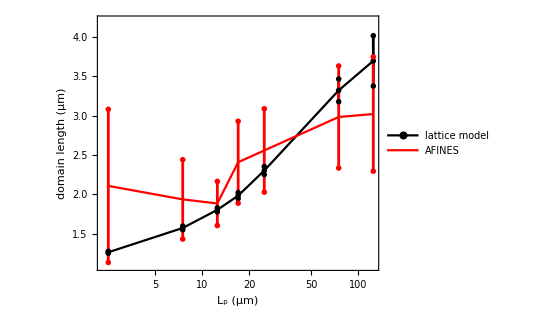

```mathematica
curves=Join[domlensL,(*domlensA,*)sdoms]; 
cols={Black,Red,Red};
pms=Join[
errbarpms[cols[[1]],Disk[],0.04],
errbarpms[cols[[2]],{Transparent,EdgeForm[Directive[Thick,cols[[2]]]],Rectangle[]}],
errbarpms[cols[[2]],{Transparent,EdgeForm[Directive[Thick,cols[[2]]]],Disk[]}]
];
labels={"lattice model","AFINES" };
p1=ListLogLinearPlot[curves,
PlotStyle->Flatten[ConstantArray[#,3]&/@cols],
Joined->{True,False,False},
PlotMarkers->pms,
Filling->Flatten[Table[{i->{i+1}},{i,2,Length[curves],3}]],
FillingStyle->fs,
PlotRange->(*Full*){Automatic,{1.1,4.2}},
FrameLabel->{"L_p (μm)","domain length (μm)"},
PlotLegends->Placed[LineLegend[riffleNones[labels],LegendLayout->"Column",LegendMarkerSize->{30,15},LegendMarkers->riffleNones[pms[[{1,4,7}]]],Spacings->0],{0.35,0.75}]]
```

```mathematica
Export[figdir<>"/mar19/lp_lgrow0_kexv0.08.pdf",p1];
Export[figdir<>"/mar19/fig2c.pdf",p1];
```

## fig 5A : growing filaments

```mathematica
densrats={0.5,1,2};
s2dens="0.25";
s1denss=densrats (ToExpression@s2dens);
s1densstrs=Map[NumberForm[#,{3,3}]&,s1denss];
```

### frames (5A)

```mathematica
seeds={5,4,1};
ts={100,200,400,650};
dirs=Table[StringJoin[ToString/@{
outdir,"/xlink_segregation/spacers/kgrow_diff0.100_maxlinks15_s1koff10.05_s2init/seed",seeds[[i]],"e7/lgrow0.040_s1dens",s1densstrs[[i]]}],{i,Length[seeds]}];
```

```mathematica
links=pts4[#,"links"][[ts]]&/@dirs;
conn1s=pts4[#,"spacers1_bound"][[ts]]&/@dirs;
conn2s=pts4[#,"spacers2_bound"][[ts]]&/@dirs;
```

```mathematica
(*centering filaments and xlinks to middle of frame*)
zeros=Table[Join[links[[i,t,1,1;;2]],{0,0}],{i,Length[links]},{t,Length[links[[i]]]}];
fov={35,20};

lc=Table[Join[rijP[links[[i,t,l,1;;2]]-links[[i,t,1,1;;2]],fov],links[[i,t,l,3;;]]],{i,Length[links]},{t,Length[links[[i]]]},{l,Length[links[[i,t]]]}];
s1c=Table[Join[rijP[conn1s[[i,t,l,1;;2]]-links[[i,t,1,1;;2]],fov],conn1s[[i,t,l,3;;]]],{i,Length[conn1s]},{t,Length[conn1s[[i]]]},{l,Length[conn1s[[i,t]]]}];
s2c=Table[Join[rijP[conn2s[[i,t,l,1;;2]]-links[[i,t,1,1;;2]],fov],conn2s[[i,t,l,3;;]]],{i,Length[conn2s]},{t,Length[conn2s[[i]]]},{l,Length[conn2s[[i,t]]]}];
```

```mathematica
frs=Table[drawmixed[{},links[[i]],conn1s[[i]],conn2s[[i]],"",False,{35,20},False,26,Green,Red,Darker[Cyan]],{i,Length[links]}];
```

```mathematica
frsc=Table[drawmixed[{},lc[[i]],s1c[[i]],s2c[[i]],"",False,{35,20},True,26,Green,Red,Darker[Cyan],"",White,-1,3,False],{i,Length[links]}];
```

```mathematica
GraphicsGrid[frscᵀ]
```

```mathematica
Do[Export[figdir<>"/diff100_frames/densrat"<>ToString[densrats[[i]]]<>"_t"<>ToString[ts[[j]]]<>"a_noframe.eps",frsc[[i,j]]],{i,Length@densrats},{j,Length@ts}];
```

### averaging over seeds for growing, increasing density ratio

```mathematica
densrats={0.1,0.2,0.5,1,1.5,2,3};
s1denss=densrats (ToExpression@s2dens);
s1densstrs=Map[ToString[NumberForm[#,{3,3}]]&,s1denss];

lgrow="0.040";
ti=Ceiling[15/ToExpression@lgrow];
winlen=100;
```

```mathematica
job1="/s1dens_lgrow0.040_s2len0.227_s1init";
job2="/s1dens_lgrow0.040_s2len0.227_s2init";
job3="/s1dens_lgrow0.040_s2len0.3_s1init_dt0.00001";
job4="/s1dens_lgrow0.040_s2len0.3_s2init_dt0.00001";
avgdldir="/dom_lens/avg_err_ns_ti"<>ToString[ti]<>"_wl"<>ToString[winlen]<>"b";
t100dir="/dom_lens/ti"<>ToString[ti]<>"_wl"<>ToString[winlen]<>"b";
```

```mathematica
Do[
DomainLengthAverager[s1densstrs,ti&,winlen,headdir<>job,("/s1dens"<>#)&,("lgrow"<>lgrow<>"_dens"<>#)&,t100dir,avgdldir,domfs,se7func],
{job,{job1,job2,job3,job4}}
];
```

Creating directory /project/weare-dinner/simonfreedman/cytomod/out/xlink_segregation/spacers/s1dens_lgrow0.040_s2len0.227_s1init/dom_lens/ti375_wl100b/

Creating directory /project/weare-dinner/simonfreedman/cytomod/out/xlink_segregation/spacers/s1dens_lgrow0.040_s2len0.227_s1init/dom_lens/avg_err_ns_ti375_wl100b/

### plotting (5B)

```mathematica
(*simulation data*)
s2dens="0.25";
jobs=
{job1,job2,job3,job4};
jobs={{job1,job2},{job3,job4}};
datfs=Table[StringJoin[ToString/@{headdir,"/",jobs[[i,j]],avgdldir,"/lgrow0.040_dens",dens,
"_doms",dom,".dat"}],{i,Length[jobs]},{j,Length[jobs[[i]]]},{dom,1,2},{dens,s1densstrs}];
dps=Map[importCheck[#][[All,1]]&,datfs,{4}];


avgdps=0.5(dps[[All,1]]+dps[[All,2]]); (*avgs over init, so second index is now spacer id*)
errscaled=dps[[All,All,All,All,2]]/dps[[All,All,All,All,1]];
lens=avgdps[[All,All,All,1]];
avgerrs1=avgdps[[All,1,All,1]]*Sqrt[errscaled[[All,1,1]]^2+errscaled[[All,2,1]]^2];
avgerrs2=avgdps[[All,2,All,1]]*Sqrt[errscaled[[All,1,2]]^2+errscaled[[All,2,2]]^2];
s1doms=Table[errcurves[densrats,lens[[i,1]],avgerrs1[[i]]],{i,Length[jobs]}];
s2doms=Table[errcurves[densrats,lens[[i,2]],avgerrs2[[i]]],{i,Length[jobs]}];
```

```mathematica
(*experimental data from winkelman 2016*)
exptDat=Import[figdir<>"/expt_domain_szs.txt","Data"];
exptdoms=errcurves[exptDat[[All,1]],exptDat[[All,2]],exptDat[[All,3]]];
```

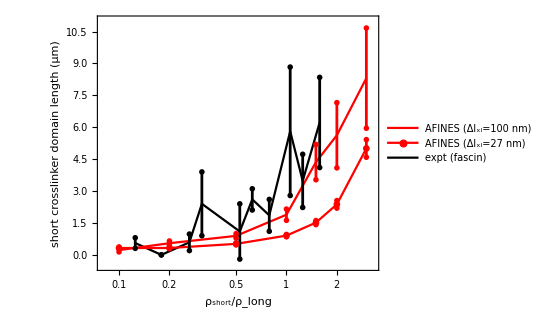

```mathematica
labels={ "expt (fascin)",
Style["AFINES (Δl_xl=27 nm)",LineSpacing->{0.2,8}],
Style["AFINES (Δl_xl=100 nm)",LineSpacing->{0.2,8}]};
cols={Black,Red,Red,Darker[Cyan]};
pms=Join[
errbarpms[cols[[1]],{Transparent,EdgeForm[Directive[Thick,cols[[1]]]],Rectangle[]}],
errbarpms[cols[[2]],{EdgeForm[Directive[Thick,cols[[2]]]],Disk[]}],
errbarpms[cols[[3]],{Transparent,EdgeForm[Directive[Thick,cols[[3]]]],Disk[]}]
];

fs=Directive[Opacity[1],Thickness[0.005]];

p1=ListLogLinearPlot[Join[exptdoms,s1doms[[1]],s1doms[[2]]],
PlotRange->{{0.08,3.3},{-0.5,11}},
PlotStyle->Flatten[ConstantArray[#,3]&/@cols],
FrameLabel->{"ρ_short/ρ_long",Style["short crosslinker\ndomain length (μm)",LineSpacing->{0.4,10}]},
Joined->{True,False,False},
PlotMarkers->pms,
Filling->Flatten[Table[{i->{i+1}},{i,2,15,3}]],
FillingStyle->fs,
PlotRange->Full,
PlotLegends->Placed[LineLegend[riffleNones[labels],LegendLayout->"ReversedColumn",LegendMarkers->riffleNones[pms[[1;;-1;;3]]],Spacings->0.1,LegendMarkerSize->{30,15}(*,LabelStyle->FontSize->18*),LabelStyle->{LineSpacing->{0.3,10},FontSize->18,TextAlignment->Left}],{0.42,0.85}(*Right*)]]
```

```mathematica
Export[figdir<>"/mar19/s1dens_rat_s1domlen_nokmc.pdf",p1];
Export[figdir<>"/mar19/fig5a.pdf",p1];
```

## Fig 5C-E, S6: Kinetics

```mathematica
lgrows1={"0.0025","0.005"};
lgrows2={"0.010","0.020","0.030","0.040","0.050","0.070","0.100"};
lgs=1000*ToExpression/@lgrows2;

domfs6k="/analysis/spacer"<>ToString[#]<>"_domains_t1-6000_nc4_rc1.dat"&/@doms;

s1koff1s={"0.05","0.1","0.2"};
jobs=Table["/kgrow_s1koff1"<>k<>"_s2kb0.0675_s"<>s<>"init",{k,s1koff1s},{s,{"1","2"}}];
```

#### averaging over seeds

```mathematica
tDoneGrowing=Ceiling[14/ToExpression@#]&;
winlen=100;
tistr="";(*"ti1500_"*);

avgdldir="/dom_lens/avg_err_ns_"<>tistr<>"wl"<>ToString[winlen]<>"b";
t100dir="/dom_lens/"<>tistr<>"wl"<>ToString[winlen]<>"b";
```

```mathematica
Do[
DomainLengthAverager[lgrows1,tDoneGrowing,winlen,headdir<>jobs[[1,i]],("/lgrow"<>#<>"_s1dens0.250")&,"lgrow"<>#<>"_dens0.250"&,t100dir,avgdldir,domfs6k,se7func],{i,2}
];
```

```mathematica
Do[
DomainLengthAverager[lgrows2,tDoneGrowing,winlen,headdir<>job,("/lgrow"<>#<>"_s1dens0.250")&,"lgrow"<>#<>"_dens0.250"&,t100dir,avgdldir,domfs,se7func],{job,Flatten[jobs]}
];
```

Creating directory /project/weare-dinner/simonfreedman/cytomod/out/xlink_segregation/spacers/kgrow_s1koff10.05_s2kb0.0675_s1init/dom_lens/wl100b/

Creating directory /project/weare-dinner/simonfreedman/cytomod/out/xlink_segregation/spacers/kgrow_s1koff10.05_s2kb0.0675_s1init/dom_lens/avg_err_ns_wl100b/

CreateDirectory::filex: /project/weare-dinner/simonfreedman/cytomod/out/xlink_segregation/spacers/kgrow_s1koff10.05_s2kb0.0675_s1init/dom_lens/wl100b/ already exists.

CreateDirectory::filex: /project/weare-dinner/simonfreedman/cytomod/out/xlink_segregation/spacers/kgrow_s1koff10.05_s2kb0.0675_s1init/dom_lens/avg_err_ns_wl100b/ already exists.

Creating directory /project/weare-dinner/simonfreedman/cytomod/out/xlink_segregation/spacers/kgrow_s1koff10.05_s2kb0.0675_s2init/dom_lens/wl100b/

Creating directory /project/weare-dinner/simonfreedman/cytomod/out/xlink_segregation/spacers/kgrow_s1koff10.05_s2kb0.0675_s2init/dom_lens/avg_err_ns_wl100b/

CreateDirectory::filex: /project/weare-dinner/simonfreedman/cytomod/out/xlink_segregation/spacers/kgrow_s1koff10.05_s2kb0.0675_s2init/dom_lens/wl100b/ already exists.

General::stop: Further output of CreateDirectory::filex will be suppressed during this calculation.

Creating directory /project/weare-dinner/simonfreedman/cytomod/out/xlink_segregation/spacers/kgrow_s1koff10.1_s2kb0.0675_s1init/dom_lens/wl100b/

Creating directory /project/weare-dinner/simonfreedman/cytomod/out/xlink_segregation/spacers/kgrow_s1koff10.1_s2kb0.0675_s1init/dom_lens/avg_err_ns_wl100b/

Creating directory /project/weare-dinner/simonfreedman/cytomod/out/xlink_segregation/spacers/kgrow_s1koff10.1_s2kb0.0675_s2init/dom_lens/wl100b/

Creating directory /project/weare-dinner/simonfreedman/cytomod/out/xlink_segregation/spacers/kgrow_s1koff10.1_s2kb0.0675_s2init/dom_lens/avg_err_ns_wl100b/

Creating directory /project/weare-dinner/simonfreedman/cytomod/out/xlink_segregation/spacers/kgrow_s1koff10.2_s2kb0.0675_s1init/dom_lens/wl100b/

Creating directory /project/weare-dinner/simonfreedman/cytomod/out/xlink_segregation/spacers/kgrow_s1koff10.2_s2kb0.0675_s1init/dom_lens/avg_err_ns_wl100b/

Creating directory /project/weare-dinner/simonfreedman/cytomod/out/xlink_segregation/spacers/kgrow_s1koff10.2_s2kb0.0675_s2init/dom_lens/wl100b/

Creating directory /project/weare-dinner/simonfreedman/cytomod/out/xlink_segregation/spacers/kgrow_s1koff10.2_s2kb0.0675_s2init/dom_lens/avg_err_ns_wl100b/

```mathematica
winlen=100;
tistr="ti1500_";

avgdldir="/dom_lens/avg_err_ns_"<>tistr<>"wl"<>ToString[winlen]<>"b";
t100dir="/dom_lens/"<>tistr<>"wl"<>ToString[winlen]<>"b";
```

```mathematica
Do[
DomainLengthAverager[lgrows2,1500&,winlen,headdir<>job,("/lgrow"<>#<>"_s1dens0.250")&,"lgrow"<>#<>"_dens0.250"&,t100dir,avgdldir,domfs,se7func],{job,Flatten[jobs]}
];
```

Creating directory /project/weare-dinner/simonfreedman/cytomod/out/xlink_segregation/spacers/kgrow_s1koff10.05_s2kb0.0675_s1init/dom_lens/ti1500_wl100b/

Creating directory /project/weare-dinner/simonfreedman/cytomod/out/xlink_segregation/spacers/kgrow_s1koff10.05_s2kb0.0675_s1init/dom_lens/avg_err_ns_ti1500_wl100b/

Creating directory /project/weare-dinner/simonfreedman/cytomod/out/xlink_segregation/spacers/kgrow_s1koff10.05_s2kb0.0675_s2init/dom_lens/ti1500_wl100b/

Creating directory /project/weare-dinner/simonfreedman/cytomod/out/xlink_segregation/spacers/kgrow_s1koff10.05_s2kb0.0675_s2init/dom_lens/avg_err_ns_ti1500_wl100b/

Creating directory /project/weare-dinner/simonfreedman/cytomod/out/xlink_segregation/spacers/kgrow_s1koff10.1_s2kb0.0675_s1init/dom_lens/ti1500_wl100b/

Creating directory /project/weare-dinner/simonfreedman/cytomod/out/xlink_segregation/spacers/kgrow_s1koff10.1_s2kb0.0675_s1init/dom_lens/avg_err_ns_ti1500_wl100b/

Creating directory /project/weare-dinner/simonfreedman/cytomod/out/xlink_segregation/spacers/kgrow_s1koff10.1_s2kb0.0675_s2init/dom_lens/ti1500_wl100b/

Creating directory /project/weare-dinner/simonfreedman/cytomod/out/xlink_segregation/spacers/kgrow_s1koff10.1_s2kb0.0675_s2init/dom_lens/avg_err_ns_ti1500_wl100b/

Creating directory /project/weare-dinner/simonfreedman/cytomod/out/xlink_segregation/spacers/kgrow_s1koff10.2_s2kb0.0675_s1init/dom_lens/ti1500_wl100b/

Creating directory /project/weare-dinner/simonfreedman/cytomod/out/xlink_segregation/spacers/kgrow_s1koff10.2_s2kb0.0675_s1init/dom_lens/avg_err_ns_ti1500_wl100b/

Creating directory /project/weare-dinner/simonfreedman/cytomod/out/xlink_segregation/spacers/kgrow_s1koff10.2_s2kb0.0675_s2init/dom_lens/ti1500_wl100b/

Creating directory /project/weare-dinner/simonfreedman/cytomod/out/xlink_segregation/spacers/kgrow_s1koff10.2_s2kb0.0675_s2init/dom_lens/avg_err_ns_ti1500_wl100b/

```mathematica
(*todeletedirs1=Import["~/Code/cytomod/spacer_metadata/"<>job<>"/crashed.txt","Table"][[All,1]];*)
```

### plotting (5C,5E,S6)

```mathematica
(*simulation data*)
lgrowsi={Join[lgrows1,lgrows2],lgrows2,lgrows2,lgrows2};
lgsi=Map[1000*ToExpression[#]&,lgrowsi,{2}];

avgdldir="/dom_lens/avg_err_ns_wl100b";
datfs1=Table[StringJoin[ToString/@{headdir,jobs[[i,s]],avgdldir,"/lgrow",lg,"_dens0.250_doms",dom,".dat"}],{i,Length[jobs]},{s,2},{dom,1,2},{lg,lgrowsi[[i]]}];

avgdldir="/dom_lens/avg_err_ns_ti1500_wl100b";
datfs2=Table[StringJoin[ToString/@{headdir,jobs[[i,s]],avgdldir,"/lgrow",lg,"_dens0.250_doms",dom,".dat"}],{i,1},{s,2},{dom,1,2},{lg,lgrows2}];

datfs=Join[datfs1,datfs2];

dps=Map[importCheck[#][[All,1]]&,datfs,{4}];
```

Data measured by Cristian:
0.75 uM actin == > kgrow = 22.15 ± 3.78 nm/s
1.5 uM actin == > kgrow = 46.99 ± 3.62 nm/s

```mathematica
k1=22.15;
k2=46.99;
line1=Line[{{Log@k1,0},{Log@k1,10}}];
line2=Line[{{Log@k2,0},{Log@k2,10}}];
```

```mathematica
(*averaging s1init with s2init -- 2nd index*)
(*indexes: koff,init,spacer id,lg*)
avgdps=0.5(dps[[All,1]]+dps[[All,2]]); (*avgs over init, so second index is now spacer id*)
errscaled=dps[[All,All,All,All,2]]/dps[[All,All,All,All,1]];
lens=avgdps[[All,All,All,1]];
avgerrs1=avgdps[[All,1,All,1]]*Sqrt[errscaled[[All,1,1]]^2+errscaled[[All,2,1]]^2];
avgerrs2=avgdps[[All,2,All,1]]*Sqrt[errscaled[[All,1,2]]^2+errscaled[[All,2,2]]^2];
s1doms=Table[errcurves[lgsi[[i]],lens[[i,1]],avgerrs1[[i]]],{i,Length[lgsi]}];
s2doms=Table[errcurves[lgsi[[i]],lens[[i,2]],avgerrs2[[i]]],{i,Length[lgsi]}];
```

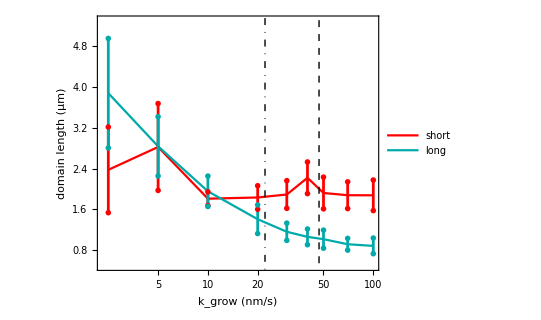

```mathematica
p2=ListLogLinearPlot[Join[s1doms[[1]],s2doms[[1]]],
PlotStyle->pss,
FrameLabel->{"k_grow (nm/s)","domain length (μm)"},
Joined->{True,False,False},
PlotMarkers->pms,
Filling->Flatten[Table[{i->{i+1}},{i,2,15,3}]],
FillingStyle->fs,
PlotRange->{Automatic,{0.5,5.3}},
PlotLegends->Placed[LineLegend[riffleNones[labels],LegendLayout->"Column",LegendMarkers->riffleNones[pms[[1;;-1;;3]]],Spacings->0,LegendMarkerSize->{30,15},LabelStyle->FontSize->18],{0.4,0.85}],
Epilog->{{Directive[Dashed,Thick],line2},{Directive[DotDashed,Thick],line1}}
]
```

```mathematica
Export[figdir<>"/mar19/kgrow_s2kb0.0675_koff1rat4_ylim_lines.pdf",p1];
Export[figdir<>"/mar19/fig5C.pdf",p1];
```

S5

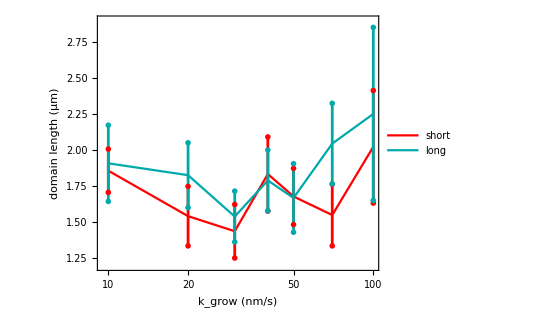

```mathematica
p1=ListLogLinearPlot[Join[s1doms[[4]],s2doms[[4]]],
PlotStyle->pss,
FrameLabel->{"k_grow (nm/s)","domain length (μm)"},
Joined->{True,False,False},
PlotMarkers->pms,
Filling->Flatten[Table[{i->{i+1}},{i,2,15,3}]],
FillingStyle->fs,
PlotRange->{Automatic,{1.2,2.9}},
PlotLegends->Placed[LineLegend[riffleNones[labels],LegendLayout->"Column",LegendMarkers->riffleNones[pms[[1;;-1;;3]]],Spacings->0,LegendMarkerSize->{30,15},LabelStyle->FontSize->18],{0.4,0.85}]
]
```

```mathematica
Export[figdir<>"/mar19/figS5.pdf",p1];
```

5 E

```mathematica
os=4.5;
lbreak=5;

line3=Line[{{0,lbreak},{100,lbreak}}];
offset=ConstantArray[{0,os},Dimensions[s1doms[[2]]][[1;;2]]];

mtix0={1.,2.,3.,4.};
mtix=Join[mtix0,mtix0+os];
tixy=Table[{i,If[MemberQ[mtix,i],ToString@Round@If[i>lbreak,i-os,i],""],If[MemberQ[mtix,i],{0.02,0},If[Mod[i,0.5]==0,{0.01,0},0]]},{i,Range[0,10,0.5]}];
```

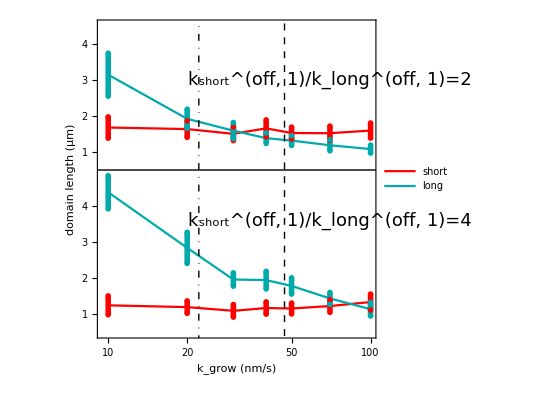

```mathematica
p1=ListLogLinearPlot[Join[s1doms[[2]]+offset,s2doms[[2]]+offset,s1doms[[3]],s2doms[[3]]],
PlotStyle->pss,
FrameLabel->{"k_grow (nm/s)","domain length (μm)"},
FrameTicks->{{tixy,Automatic},Automatic},
Joined->{True,False,False},
PlotMarkers->pms,
Filling->Flatten[Table[{i->{i+1}},{i,2,15,3}]],
FillingStyle->fs,
PlotRange->{Automatic,{0.5,9}},
PlotLegends->Placed[LineLegend[riffleNones[labels],LegendLayout->"Column",LegendMarkers->riffleNones[pms[[1;;-1;;3]]],Spacings->0,LegendMarkerSize->{30,15},LabelStyle->FontSize->18],{0.2,0.9}(*Right*)],
Epilog->{Inset[Style["k_short^(off, 1)/k_long^(off, 1)=4",FontSize->18],{Log@70,3.6}],
,Inset[Style["k_short^(off, 1)/k_long^(off, 1)=2",FontSize->18],{Log@70,7.5}],
{Directive[Dashed,Thick],line2},
{Directive[DotDashed,Thick],line1},
{Directive[Thick],line3}},
AspectRatio->1
]
```

```mathematica
Export[figdir<>"/mar19/kgrow_s2kb0.0675_koff1rat2-4_stacked_lines.pdf",p1];
Export[figdir<>"/mar19/fig5E.pdf",p1];
```

### Print data

```mathematica
idx=3;
```

```mathematica
{s1doms[[idx,1,All,1]],s1doms[[idx,1,All,2]],s1doms[[idx,1,All,2]]-s1doms[[idx,2,All,2]]}ᵀ//TableForm
```

10. | 1.23844 | 0.262253
20. | 1.18873 | 0.174148
30. | 1.08576 | 0.175147
40. | 1.16316 | 0.171321
50. | 1.15002 | 0.152466
70. | 1.218 | 0.174966
100. | 1.32972 | 0.223699

```mathematica
{s2doms[[idx,1,All,2]],s2doms[[idx,1,All,2]]-s2doms[[idx,2,All,2]]}ᵀ//TableForm
```

4.38132 | 0.461962
2.83597 | 0.432844
1.95578 | 0.186426
1.93948 | 0.246084
1.7776 | 0.227243
1.43057 | 0.168097
1.13041 | 0.189162

## Fig S1: testing domain calculation

### calculation steps

```mathematica
fidx=0;
dir=outdir<>"/xlink_segregation/spacers/denstot_0.5_s2init/seed3e7/lgrow0_s1dens0.250";
t=500;
fov={35,20};
lmax=15;
l0=0.037;
```

```mathematica
lks=pts4[dir,"links"];
flks=Map[Cases[#,_?((#[[5]]==fidx)&)]&,lks];
conn1s=pts4[dir,"spacers1_bound"];
conn2s=pts4[dir,"spacers2_bound"];
```

```mathematica
d1=Table[distFromBarbedEnd[flks[[t]],fidx,conn1s[[t,i]],fov],{i,Length[conn1s[[t]]]}];
d2=Table[distFromBarbedEnd[flks[[t]],fidx,conn2s[[t,i]],fov],{i,Length[conn2s[[t]]]}];
bcs1=BinCounts[d1,{0,lmax,l0}];
bcs2=BinCounts[d2,{0,lmax,l0}];
lattice=Sign[bcs1-bcs2]/.{-1->2};
pos1=Flatten[Position[lattice,1]];
pos2=Flatten[Position[lattice,2]];
```

```mathematica
dom1s=Map[ToExpression,importCheck[dir<>domfs[[1]]],{3}];
dom2s=Map[ToExpression,importCheck[dir<>domfs[[2]]],{3}];
```

```mathematica
xs=(Range[Length[bcs1]]-1)*l0;
dom1st=dom1s[[t,1]];
dom2st=dom2s[[t,1]];
n1=Length[dom1st];
n2=Length[dom2st];
```

```mathematica
Union[bcs2]
```

{0,1,2}

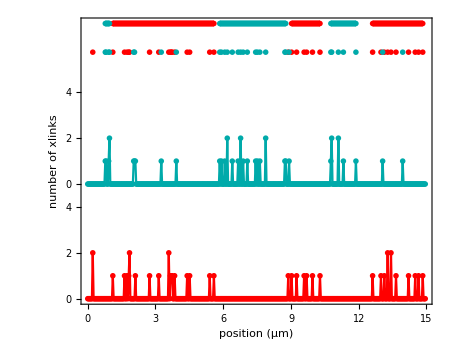

```mathematica
p1=ListPlot[Join[{{xs,bcs1}ᵀ,{xs,bcs2+5}ᵀ,
constFun[(pos1-1)*l0,10.75],constFun[(pos2-1)*l0,10.75]},
Table[constFun[dom1st[[i,{1,-1}]],12],{i,Length[dom1st]}],
Table[constFun[dom2st[[i,{1,-1}]],12],{i,Length[dom2st]}]],
Joined->Join[{True,True,False,False},ConstantArray[True,n1+n2]],
PlotStyle->Join[cols,cols,ConstantArray[Directive[cols[[1]],Thickness[0.01]],n1],ConstantArray[Directive[cols[[2]],Thickness[0.01]],n2]],
PlotMarkers->Join[
{Null,Null,{vline[0.05],0.07},{vline[0.05],0.07}},ConstantArray[{vline[0.5],0.05},n1+n2]
],
FrameLabel->{"position (μm)","number of xlinks\t"},
FrameTicks->{{{{0,c1@0},{1,""},{2,c1@2},{3,""},{4,c1@4},{5,c2@0},{6,""},{7,c2@2},{8,""},{9,c2@4},{10,""}},Join[constFun[Range[10],""],{{10.75,"label",0},{12,"domain",0}}]},Automatic},ImageSize->450]
```

```mathematica
Export[figdir<>"/domain_testing.eps",p1];
```

```mathematica
Export[figdir<>"/S1.eps",p1];
```

## more movies

```mathematica
koffs={"0.05","0.10"};
lgrows={"0.010","0.100"};
```

```mathematica
idxs={1,2};
```

```mathematica
idxs={3,6,9};
sidx=1;

job="kgrow_s1koff10.1_s2kb0.0675_s1init";
lgrows={"0.0025","0.005","0.010","0.020","0.030","0.040","0.050","0.070","0.100"};

dirs=Table[StringJoin[ToString/@{
outdir,"/xlink_segregation/spacers/"<>job<>"/seed"<>ToString[i]<>"e7/lgrow",lgrow,"_s1dens0.250"}],{lgrow,lgrows},{i,seeds}];
dirs=DeleteCases[dirs,Apply[Alternatives,todeletedirs],{2}];
```

```mathematica
dirs[[idxs,sidx]]
```

{/project/weare-dinner/simonfreedman/cytomod/out/xlink_segregation/spacers/kgrow_s1koff10.1_s2kb0.0675_s1init/seed1e7/lgrow0.010_s1dens0.250,/project/weare-dinner/simonfreedman/cytomod/out/xlink_segregation/spacers/kgrow_s1koff10.1_s2kb0.0675_s1init/seed1e7/lgrow0.040_s1dens0.250,/project/weare-dinner/simonfreedman/cytomod/out/xlink_segregation/spacers/kgrow_s1koff10.1_s2kb0.0675_s1init/seed1e7/lgrow0.100_s1dens0.250}

```mathematica
links=pts4[#,"links"]&/@(dirs[[idxs,sidx]]);
conn1s=pts4[#,"spacers1_bound"]&/@(dirs[[idxs,sidx]]);
conn2s=pts4[#,"spacers2_bound"]&/@(dirs[[idxs,sidx]]);
```

```mathematica
linkz=Table[Map[myrijP[#,links[[i,1,1,1;;2]],{35,20}]&,links[[i]],{2}],{i,Length[idxs]}];
conn1z=Table[Map[myrijP[#,links[[i,1,1,1;;2]],{35,20}]&,conn1s[[i]],{2}],{i,Length[idxs]}];
conn2z=Table[Map[myrijP[#,links[[i,1,1,1;;2]],{35,20}]&,conn2s[[i]],{2}],{i,Length[idxs]}];
```

```mathematica
tfs=Round/@(14/ToExpression/@(lgrows[[idxs]])+100);
dt=5;
idxs2=Table[Range[1,tf,dt],{tf,tfs}];
nts=Max[Length/@idxs2];
idxs2=Table[PadRight[idxs2[[i]],nts,idxs2[[i,-1]]],{i,Length[idxs2]}];
```

```mathematica
mov=Table[drawmixed[{},linkz[[i,idxs2[[i]]]],conn1z[[i,idxs2[[i]]]],conn2z[[i,idxs2[[i]]]],"",False,{35,20},False,26,Green,Red,Darker[Cyan],White,"",-1,3,False],{i,Length[idxs]}];
```

```mathematica
outf="s1koff0-05_lgrow2-5_10_40_100_s"<>ToString@sidx;
outf="s1koff0-1_lgrow10_40_100_s"<>ToString@sidx;
trimovie=Table[GraphicsRow[Table[mov[[i,t]],{i,Length[idxs]}],Frame->All,Spacings->0],{t,Dimensions[mov][[2]]}];
Export[figdir<>"/"<>outf<>".avi",trimovie,ImageResolution->250];
```

```mathematica
GraphicsRow[{mov[[1,1500]],mov[[2,240]]}]
```

```mathematica
tfslow=1500;
tffast=240;
mov2stop=Join[mov[[2,1;;tffast]],ConstantArray[mov[[2,tffast]],tfslow-tffast]];
```

```mathematica
Dimensions[mov2stop]
```

{1500}

```mathematica
dimovie=Table[GraphicsRow[{mov[[1,t]],mov[[2,t]]},Frame->All,Spacings->0],{t,Dimensions[mov][[2]]}];
```

```mathematica
dimovieStop=Table[GraphicsRow[{mov[[1,t]],mov2stop[[t]]},Frame->All,Spacings->0],{t,tfslow}];
```

```mathematica
Export[figdir<>"/lgrows10_100_koff1_s6_100s.avi",dimovieStop];
```